```mathematica
A[ψ_]:=Simplify[Sqrt[α/2](x ψ-D[ψ,x]/α)]
a[ψ_]:=Simplify[Sqrt[α/2](x ψ+D[ψ,x]/α)]
ψ0=Sqrt[Sqrt[α/Pi]]Exp[-α/2 x^2]
ψ1=A[ψ0]
ψ2=A[ψ1]/Sqrt[2]
ψ3=A[ψ2]/Sqrt[3]
ψ4=A[ψ3]/Sqrt[4]
ψ5=A[ψ4]/Sqrt[5]
ψ6=A[ψ5]/Sqrt[6]
ψ7=A[ψ6]/Sqrt[7]
```

(ⅇ^(-(x^2 α)/2) α^(1/4))/π^(1/4)

(√2 ⅇ^(-(x^2 α)/2) x α^(3/4))/π^(1/4)

(ⅇ^(-(x^2 α)/2) α^(1/4) (-1+2 x^2 α))/(√2 π^(1/4))

(ⅇ^(-(x^2 α)/2) x α^(3/4) (-3+2 x^2 α))/(√3 π^(1/4))

(ⅇ^(-(x^2 α)/2) α^(1/4) (3-12 x^2 α+4 x^4 α^2))/(2 √6 π^(1/4))

(ⅇ^(-(x^2 α)/2) x α^(3/4) (15-20 x^2 α+4 x^4 α^2))/(2 √15 π^(1/4))

(ⅇ^(-(x^2 α)/2) α^(1/4) (-15+90 x^2 α-60 x^4 α^2+8 x^6 α^3))/(12 √5 π^(1/4))

(ⅇ^(-(x^2 α)/2) x α^(3/4) (-105+210 x^2 α-84 x^4 α^2+8 x^6 α^3))/(6 √70 π^(1/4))

(ⅇ^(-x^2/2))/π^(1/4)

(√2 ⅇ^(-x^2/2) x)/π^(1/4)

(ⅇ^(-x^2/2) (-1+2 x^2))/(√2 π^(1/4))

(ⅇ^(-x^2/2) x (-3+2 x^2))/(√3 π^(1/4))

(ⅇ^(-x^2/2) (3-12 x^2+4 x^4))/(2 √6 π^(1/4))

(ⅇ^(-x^2/2) x (15-20 x^2+4 x^4))/(2 √15 π^(1/4))

(ⅇ^(-x^2/2) (-15+90 x^2-60 x^4+8 x^6))/(12 √5 π^(1/4))

(ⅇ^(-x^2/2) x (-105+210 x^2-84 x^4+8 x^6))/(6 √70 π^(1/4))

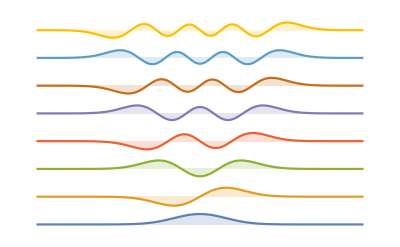

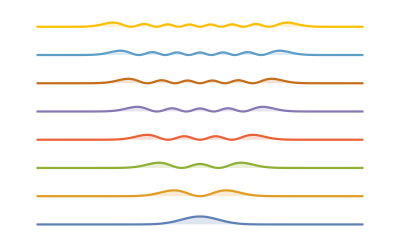

```mathematica
AA[ψ_]:=Simplify[Sqrt[1/2](x ψ-D[ψ,x])]
aa[ψ_]:=Simplify[Sqrt[1/2](x ψ+D[ψ,x])]
y0=Sqrt[Sqrt[1/Pi]]Exp[-1/2 x^2]
y1=AA[y0]
y2=AA[y1]/Sqrt[2]
y3=AA[y2]/Sqrt[3]
y4=AA[y3]/Sqrt[4]
y5=AA[y4]/Sqrt[5]
y6=AA[y5]/Sqrt[6]
y7=AA[y6]/Sqrt[7]
Plot[{y0,y1+2,y2+4,y3+6,y4+8,y5+10,y6+12,y7+14},{x,-2Pi,2Pi},PlotRange->All,Axes->False,Filling->{1->0,2->2,3->4,4->6,5->8,6->10,7->12,8->14}]
Plot[{y0^2,y1^2+2,y2^2+4,y3^2+6,y4^2+8,y5^2+10,y6^2+12,y7^2+14},{x,-2Pi,2Pi},PlotRange->All,Axes->False,Filling->{1->0,2->2,3->4,4->6,5->8,6->10,7->12,8->14}]
```

```mathematica
AAA[ψ_]:=Simplify[Sqrt[α/2](x ψ-D[ψ,x]/α)]
aaa[ψ_]:=Simplify[Sqrt[α/2](x ψ+D[ψ,x]/α)]
ψy0=Sqrt[Sqrt[α/Pi]]Exp[-α/2 x^2]
ψy1=AAA[ψy0]
ψy2=AAA[ψy1]/Sqrt[2]
ψy3=AAA[ψy2]/Sqrt[3]
ψy4=AAA[ψy3]/Sqrt[4]
ψy5=AAA[ψy4]/Sqrt[5]
ψy6=AAA[ψy5]/Sqrt[6]
ψy7=AAA[ψy6]/Sqrt[7]
```

(ⅇ^(-(x^2 α)/2) α^(1/4))/π^(1/4)

(√2 ⅇ^(-(x^2 α)/2) x α^(3/4))/π^(1/4)

(ⅇ^(-(x^2 α)/2) α^(1/4) (-1+2 x^2 α))/(√2 π^(1/4))

(ⅇ^(-(x^2 α)/2) x α^(3/4) (-3+2 x^2 α))/(√3 π^(1/4))

(ⅇ^(-(x^2 α)/2) α^(1/4) (3-12 x^2 α+4 x^4 α^2))/(2 √6 π^(1/4))

(ⅇ^(-(x^2 α)/2) x α^(3/4) (15-20 x^2 α+4 x^4 α^2))/(2 √15 π^(1/4))

(ⅇ^(-(x^2 α)/2) α^(1/4) (-15+90 x^2 α-60 x^4 α^2+8 x^6 α^3))/(12 √5 π^(1/4))

(ⅇ^(-(x^2 α)/2) x α^(3/4) (-105+210 x^2 α-84 x^4 α^2+8 x^6 α^3))/(6 √70 π^(1/4))

```mathematica
Integrate[ψy0^2,{x,-Infinity,Infinity}]
Integrate[ψy1^2,{x,-Infinity,Infinity}]
Integrate[ψy2^2,{x,-Infinity,Infinity}]
Integrate[ψy3^2,{x,-Infinity,Infinity}]
Integrate[ψy4^2,{x,-Infinity,Infinity}]
Integrate[ψy5^2,{x,-Infinity,Infinity}]
Integrate[ψy6^2,{x,-Infinity,Infinity}]
Integrate[ψy7^2,{x,-Infinity,Infinity}]
```